## 3.029 Spring 2022 Lecture 05 - 02/14/2022

## Convexity of Thermodynamic Potentials

You have probably already seen two very important thermodynamic potentials in 3.020

Internal Energy,

Entropy,

This week in 3.020, I believe you will introduce new thermodynamic potentials such as:

Enthalpy,

Helmholtz Free Energy,  (note: some books use the symbol )

Gibbs Free Energy,

In today’s lecture, we’ll jump the gun a bit and introduce some postulates of Thermodynamic potentials, to allow us to continue our discussion on the Van der Waals gas

Note: This approach can be termed ‘phenomenological thermodynamics’ and follows the treatment of Callen - nicely summarized by this short paper: https://arxiv.org/pdf/1404.5273.pdf

## Phenomenological Thermodynamics

A thermodynamic system is completely characterized by the following thermodynamic variables:

Extensive

Mole number of component ,

Volume,

Entropy,

Internal Energy,

Intensive

Chemical potential of component ,

Pressure,

Temperature,

The intensive variables are related by an equation of state

This function is convex in

i.e. its second derivative w.r.t.  is nonnegative

You’ll notice this is not exactly in the form of the ideal gas law we saw last time: 
We will use the next postulate to “change variables”

For all intensive variables , the internal energy  satisfies the Euler equality

In 3.020 you will see that you can combine the first and second laws of thermodynamics to obtain a useful relation 
this is often referred to as the fundamental thermodynamic relation

However, we can also take a total differential of the Euler equality

Setting the two definitions equal to each other, we obtain constraints on the intensive variables

This is known as the Gibbs-Duhem relation

Let’s think about this for a second - consider a binary system at constant temperature and pressure 
This simplifies the Gibbs-Duhem relation to read: 
Varying the chemical potential of one component automatically causes the chemical potential of the other component to change in the opposite direction, 
and this rate of this change is related to the mole numbers of the two components in the system.

### Thermodynamic Potentials

Depending on the experimental conditions we’re interested in, we can re-cast the fundamental thermodynamic relation in more natural variables.

Starting with the internal energy

its natural variables are:

Entropy,

Volume,

Mole numbers,

We can easily re-arrange this for entropy

with natural variables:

Internal Energy, U

Volume,

Mole numbers,

To get the other thermodynamic potentials, like Helmholtz and Gibbs Free Energies, we need to do a bit more work

Rigorously, the transformation we’ll use is called a Legendre Transform and we’ll talk more about it next lecture 
(I promise you have seen this in at-least two different contexts so far in your studies!)

We will sketch out the procedure today:

If we want to transform the internal energy such that a new intensive variable  is a natural variable, we start by defining a new potential as the difference of the internal energy with the product of this intensive variable and its extensive conjugate

We then take the total differential of our new thermodynamic potential

And finally, use the fundamental thermodynamic relation to substitute for  and simplify our expression

#### Examples

Let’s say we wanted to express the thermodynamic potential with Temperature as a natural variable (whose extensive conjugate is Entropy)

This thermodynamic is called the Helmholtz Free Energy with natural variables:

Temperature, T

Volume,

Mole numbers,

Similarly, if we wanted to express the thermodynamic potential with Temperature and Pressure as a natural variables

 + P V 
 + P dV + V dP

This thermodynamic is called the Gibbs Free Energy with natural variables:

Temperature, T

Pressure, P

Mole numbers,

This is a very convenient thermodynamic potential, which you’ll encounter over and over again, because in everyday conditions temperature and pressure is approximately constant

## Thermodynamic Potentials Convexity

In our three postulates, we specified the equation of state must be convex in the intensive variables

Next lecture, we’ll see where this comes from

For now let's investigate what happens when this is not the case using our normalized Van der Waals equation of state

```mathematica
pNormalvdWEquationOfStateNormalized[vNormalized_,tNormalized_]=(3-9 vNormalized+8 tNormalized vNormalized^2)/(vNormalized^2 (-1+3 vNormalized));
```

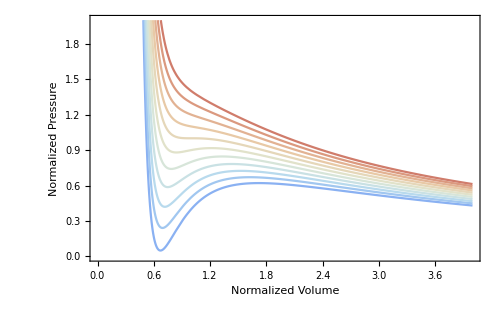

```mathematica
isothermPlot=With[ {curves = Table[pNormalvdWEquationOfStateNormalized[vNormalized,tNormalized],{tNormalized,0.85,1.1,0.025}]},
Plot[curves,{vNormalized,0.4,4},]
]
```

### Helmholtz Free Energy

The Helmholtz Free Energy for the Van der Waals gas can be derived from statistical mechanics

Where  is a constant that has units of [temperature^(3/2)/volume] and depends on Planck’s and Boltzmann’s constants.

```mathematica
helmholtzFreeEnergy[a_,b_,r_,ϕ_][molarVolume_,temperature_]=-8/3(r temperature (1+Log[(molarVolume-b)/ϕ temperature^(3/2)])+a/molarVolume);
```

We normalize the free energy by evaluating a and b at the critical values we obtained earlier

```mathematica
criticalSolutionsSubstitutions={a->(9 r tCritical vCritical)/8,b->vCritical/3}
```

{a→(9 r tCritical vCritical)/8,b→vCritical/3}

```mathematica
normalizedHelmholtzFreeEnergy[vNormalized_,tNormalized_]=FullSimplify[helmholtzFreeEnergy[(9 r tCritical vCritical)/8,vCritical/3,r,tCritical^(3/2)vCritical][vNormalized vCritical,tNormalized tCritical]/(r tCritical),Assumptions->tCritical> 0]
```

-(9+8 tNormalized vNormalized+8 tNormalized vNormalized Log[1/3 tNormalized^(3/2) (-1+3 vNormalized)])/(3 vNormalized)

And plot this for various normalized temperatures

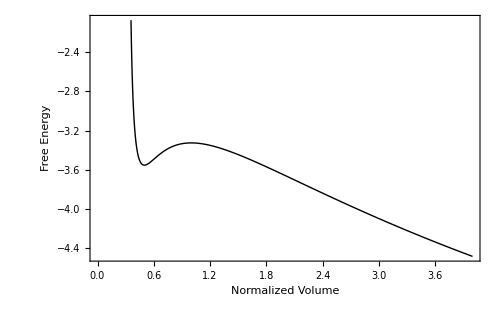

```mathematica
Plot[normalizedHelmholtzFreeEnergy[vNormalized,0.75],{vNormalized,0,4},]
```

```mathematica
Manipulate[Plot[normalizedHelmholtzFreeEnergy[vNormalized,temperature],{vNormalized,0,4},],{{temperature,0.75},0.5,1.25},Paneled->False]
```

The Helmholtz free energy develops a concavity for temperatures below the critical isotherm

Below the critical point, a common tangent can be constructed

That is, we seek to find a straight line which intersects our free energy at two points  and  and is tangent at our free energy at those points

Mathematically, this is specified by matching their derivatives according to:

```mathematica
Clear[commonTangentPoints,initialGuesses]

initialGuesses=<|0.75->{0.5,5}|>;
commonTangentPoints[temperature_?(0.75<= #<1&)]:=commonTangentPoints[temperature]=Module[{reversedGuesses,guessesV,guessesA,isotherm,sol},

reversedGuesses=AssociationMap[Reverse,initialGuesses];
guessesV=First[Nearest[reversedGuesses,temperature]];

isotherm[vNormalized_]=normalizedHelmholtzFreeEnergy[vNormalized,temperature];
guessesA=isotherm/@guessesV;

sol=Quiet@FindRoot[{
a1==isotherm[v1],
a2==isotherm[v2],
isotherm'[v1]==isotherm'[v2],
isotherm'[v1]==(a2-a1)/(v2-v1)
},
{v1,guessesV[[1]]},{v2,guessesV[[2]]},{a1,guessesA[[1]]},{a2,guessesA[[2]]}];

AssociateTo[initialGuesses,(temperature->{v1,v2})/.sol];

{
{{v1,a1},{v2,a2}}/.sol,
Piecewise[{{a1+isotherm'[v1] (vNormalized-v1),v2>vNormalized>v1}},_]/.sol
}]

commonTangentPoints[temperature_?(#>=1&)]:=With[{pts=commonTangentPoints[0.999999][[1,All,1]]},
{{#,normalizedHelmholtzFreeEnergy[#,temperature]}&/@pts,normalizedHelmholtzFreeEnergy[#,temperature]&}]
```

```mathematica
Manipulate[
With[{commonPts=commonTangentPoints[temperature]},
Show[Plot[{normalizedHelmholtzFreeEnergy[vNormalized,temperature],commonPts[[2]]},{vNormalized,0,5},],Graphics[{{PointSize[0.015],Red,Point[commonPts[[1]]]},{Dashed,Line[{{#[[1]],-10},{#[[1]],0}}]&/@commonPts[[1]]}}]]],{temperature,0.75,1.1},Paneled->False]
```

#### Gibbs Free Energy

Let’s use our Legendre transforms from above to define the Gibbs Free energy

First, remember the differential form of the Helmholtz Free energy

and use it to define the pressure at constant temperature and mole numbers

And then use our Legendre transform to define the Gibbs Free energy as

This allows us to express the GIbbs-free energy parametrically with the normalized volume as

```mathematica
parametricGibbs[vNormalized_,tNormalized_]=FullSimplify[{
-Derivative[1,0][normalizedHelmholtzFreeEnergy][vNormalized,tNormalized],normalizedHelmholtzFreeEnergy[vNormalized,tNormalized]-Derivative[1,0][normalizedHelmholtzFreeEnergy][vNormalized,tNormalized]vNormalized
}];

parametricGibbsFlipped[vNormalized_,tNormalized_]={-#2,#1}&@@parametricGibbs[vNormalized,tNormalized]
```

{6/vNormalized-(8 tNormalized)/(-3+9 vNormalized)+8/3 tNormalized Log[1/3 tNormalized^(3/2) (-1+3 vNormalized)],-3/vNormalized^2+(8 tNormalized)/(-1+3 vNormalized)}

We can now put everything together!

```mathematica
linkedVisualization[tNormalized_]:=Block[{
padding={{45,5},{45,5}},
colors={Red,RGBColor[0,1/3,0],Blue},
gibbs,helm,press
},

gibbs=ParametricPlot[parametricGibbsFlipped[vNormalized,tNormalized],{vNormalized,0,4},Frame->True,BaseStyle->14,PlotStyle->Directive[Thick,colors[[1]]],FrameLabel->{"Gibbs Free Energy","Pressure"},PlotRange->{Automatic,{0,2}},ImagePadding->padding,ImageSize->300,AspectRatio->1/2];

helm=Plot[normalizedHelmholtzFreeEnergy[vNormalized,tNormalized],{vNormalized,0,4},Frame->True,BaseStyle->14,PlotRange->{{0,4},Automatic},PlotStyle->Directive[Thick,colors[[2]]],FrameLabel->{"Volume","Free Energy"},ImagePadding->padding,ImageSize->300,AspectRatio->1/2];

press=Plot[pNormalvdWEquationOfStateNormalized[vNormalized,tNormalized],{vNormalized,0.5,4},Frame->True,PlotRange->{{0,4},{0,2}},BaseStyle->14,FrameLabel->{"Volume","Pressure"},ImagePadding->padding,ImageSize->300,PlotStyle->Directive[Thick,colors[[3]]],AspectRatio->1/2];

GraphicsGrid[{{"",helm},{gibbs,press}},ImageSize->750]

]
```

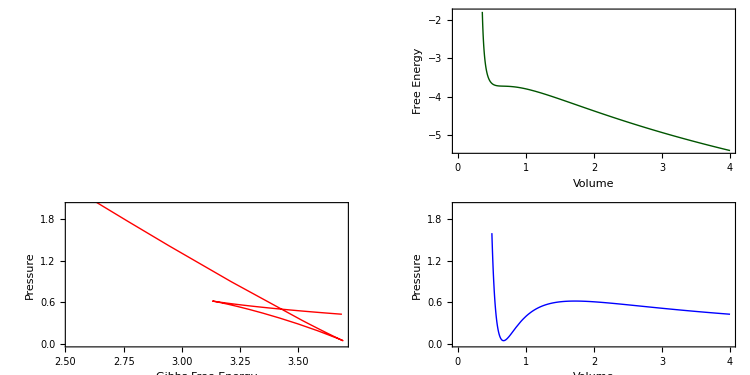

```mathematica
linkedVisualization[0.85]
```

```mathematica
Manipulate[linkedVisualization[temperature],{{temperature,1},0.85,1.1},Paneled->False]
```

Remember our condition for stability re: the isothermal bulk modulus from last lecture?

We can use the differential form of the Gibbs free energy to express the volume as:

This suggests our stability condition can be expressed in terms of the curvature of the Gibbs function:

Notice how there’s regions outside the equilibrium pressure (kink in Gibbs function), which nonetheless are thermodynamically stable

This is a common feature in many thermodynamic phenomena, which you will explore more in your second assignment

In particular, in your second assignment, you will explore yet another construction, called the Maxwell equal-area construction, to connect all these methods!